```mathematica
$Assumptions={_∈Reals, h>0, h<1};
eq1 = 1==l(i h) +b;
eq2 = 0==l(i-1)h+b;
Solve[{eq1,eq2},{l,b}]
```

{{l→1/h,b→1-i}}

```mathematica
eq3 = 0==l(i+1)h+b;
Solve[{eq1,eq3},{l,b}]
```

{{l→-1/h,b→1+i}}

```mathematica
b[x_,h_,i_]:=Piecewise[{{1/h x+(1-i), (i-1)h≤x<i h}, {-1/h x+(1+i), i h ≤ x <(i+1) h}, {0, True}}]
```

```mathematica
Integrate[b[x,1,0]*b[x,1,0],{x,0,5}]
```

1/3

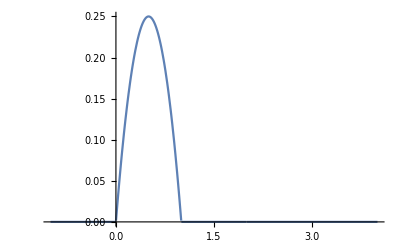

```mathematica
Plot[b[x,1,0]*b[x,1,1],{x,-1,4},PlotRange->All]
```

```mathematica
Plot3D[{b[x,1,0]*b[y,1,0]},{x,-4,4},{y,-4,4},PlotRange->All]
```

-Graphics3D-

```mathematica
Integrate[1/r b[r,h,0]b[r,h,0]b[r,h,0]4π r^2,{r,-h,h}]
```

∫_-h^h 4 π r (Piecewise[{{1+r/h, -h≤r<0}, {1-r/h, 0≤r<h}, {0, True}}])^3ⅆr

```mathematica
Integrate[1/r 4π r^2 (1/h r+(1-0)) (1/h r+(1-0)) (1/h r+(1-0)),{r,-h,0}]
```

-(h^2 π)/5

```mathematica
Integrate[1/r 4π r^2 (-1/h r+(1-0)) (-1/h r+(1-0)) (-1/h r+(1-0)),{r,0,h}]
```

(h^2 π)/5

```mathematica
(M=h/3{{1, 1/2,0,0,0},
{1/2,2,1/2,0,0},
{0,1/2,2,1/2,0},
{0,0,1/2,2,1/2},
{0,0,0,1/2,1}})//MatrixForm
```

(h/3 | h/6 | 0 | 0 | 0
h/6 | (2 h)/3 | h/6 | 0 | 0
0 | h/6 | (2 h)/3 | h/6 | 0
0 | 0 | h/6 | (2 h)/3 | h/6
0 | 0 | 0 | h/6 | h/3)

```mathematica
M.M.M//MatrixForm
```

((2 h^3)/27 | (5 h^3)/36 | (5 h^3)/108 | h^3/216 | 0
(5 h^3)/36 | (43 h^3)/108 | (17 h^3)/72 | h^3/18 | h^3/216
(5 h^3)/108 | (17 h^3)/72 | (11 h^3)/27 | (17 h^3)/72 | (5 h^3)/108
h^3/216 | h^3/18 | (17 h^3)/72 | (43 h^3)/108 | (5 h^3)/36
0 | h^3/216 | (5 h^3)/108 | (5 h^3)/36 | (2 h^3)/27)

```mathematica
LinearSolve[M.M.M,8 h^6]
```

LinearSolve[{{(2 h^3)/27,(5 h^3)/36,(5 h^3)/108,h^3/216,0},{(5 h^3)/36,(43 h^3)/108,(17 h^3)/72,h^3/18,h^3/216},{(5 h^3)/108,(17 h^3)/72,(11 h^3)/27,(17 h^3)/72,(5 h^3)/108},{h^3/216,h^3/18,(17 h^3)/72,(43 h^3)/108,(5 h^3)/36},{0,h^3/216,(5 h^3)/108,(5 h^3)/36,(2 h^3)/27}},8 h^6]

```mathematica
Integrate[x b[x,h,2],{x,0,4}]
```

∫_0^4 x (Piecewise[{{-1+x/h, h≤x<2 h}, {3-x/h, 2 h≤x<3 h}, {0, True}}])ⅆx

```mathematica
Integrate[x(-1+x/h),{x,h,2h}]+Integrate[x(3-x/h),{x,2h,3h}]
```

2 h^2

```mathematica
2 h^2 2 h^2 2 h^2
```

8 h^6